```mathematica
f=2 x^2+7 x y + 6 y^2+13 x+22y+20;
Factor[f]
```

(4+x+2 y) (5+2 x+3 y)

```mathematica
Solve[4+x+2 y==0==5+2 x+3 y,{x,y}]
```

{{x→2,y→-3}}

```mathematica
bis=Simplify[Abs[4+x+2 y]/(√(1^2+2^2))-Abs[5+2 x+3 y]/(√(2^2+3^2))]//Expand
bis2=(x^2-y^2)/(x y)-(2(2-6))/7//Expand
```

Abs[4+x+2 y]/(√5)-Abs[5+2 x+3 y]/(√13)

8/7+x/y-y/x

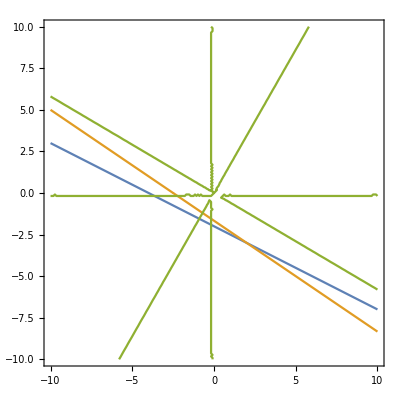

```mathematica
ContourPlot[{4+x+2 y==0,5+2 x+3 y==0,bis2==0},{x,10,-10},{y,10,-10}]
```